What is the change in kinetic energy as we change μ? In our units, changing Re_i and μ simultaneously to hold Re_o constant, how does the kinetic energy change? Does it go up or down?

```mathematica
A = (1/η -1)( μ-η^2)/(1-η^2)
```

((-1+1/η) (-η^2+μ))/(1-η^2)

```mathematica
B =η (1-μ)/((1-η)*(1-η^2))
```

(η (1-μ))/((1-η) (1-η^2))

```mathematica
V =A r + B/r
```

(η (1-μ))/(r (1-η) (1-η^2))+(r (-1+1/η) (-η^2+μ))/(1-η^2)

```mathematica
Ri = η/(1-η)
```

η/(1-η)

```mathematica
Ro = Ri/η
```

1/(1-η)

```mathematica
KE = 2 π Lz Integrate[0.5r  V^2, {r, Ri, Ro}, Assumptions->{r, η, μ} ∈ Reals && r>0 && 0<η < 1 ]
```

-(0.785398 Lz ((-1+η^2) (η^2-μ) (η^4+3 η^2 (-1+μ)-μ)+4 η^4 (-1+μ)^2 Log[η]))/((-1+η)^4 η^2 (1+η)^2)

```mathematica
Vol = π (Ro^2 - Ri^2) Lz
```

Lz π (1/(1-η)^2-η^2/(1-η)^2)

As an example, choose step 3 and step 4 on path 2 of Meseguer et al (2009):

```mathematica
KEstep1 = KE/.η->0.883/.μ->-1.875/.Lz->29.9
```

908.262

```mathematica
KEstep3 = KE /.η->0.883/.μ->-2.142857/.Lz->29.9
```

1201.02

```mathematica
KEstep4 =KE/.η->0.883/.μ->-2.2222222/.Lz->29.9
```

1297.21

```mathematica
KEstep5 = KE /.η->0.883/.μ->-2.30769/.Lz->29.9
```

1405.63

```mathematica
delta4 = KEstep4 - KEstep3
```

96.1892

```mathematica
delta5 = KEstep5 - KEstep4
```

108.414

```mathematica
Vstep3 = V/.η->0.883/.μ->-2.142857
```

107.662/r-1.75772 r

```mathematica
Vstep4 = V/.η->0.883/.μ->-2.2222222
```

110.381/r-1.80546 r

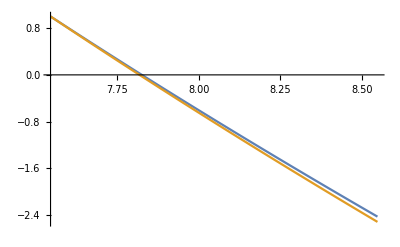

```mathematica
Plot[{ Vstep3,Vstep4}, {r, Ri/.η->0.883,Ro/.η->0.883}]
```

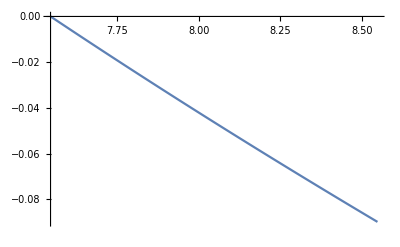

```mathematica
Plot[ Vstep4-Vstep3, {r, Ri/.η->0.883,Ro/.η->0.883}]
```